```mathematica
(* Base Tabu Inertia *)
inertiaData20 = {{5, 703.16}, {10,703.16}, {30, 703.16}};
inertiaData50 = {{5, 1103.10}, {10,1438.80}, {30, 1601.32}};
inertiaData100 = {{5, 1561.84}, {10, 1109.09}, {30,1494.35}};
```

```mathematica
iplot20= ListLinePlot[inertiaData20,
PlotStyle-> {Red}];
iplot50= ListLinePlot[inertiaData50,
PlotStyle-> {Green}];
iplot100= ListLinePlot[inertiaData100,
PlotStyle-> {Blue}];
```

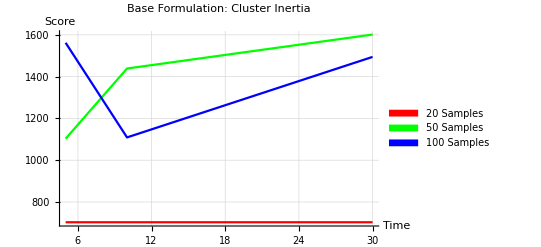

```mathematica
Legended[
Show[iplot20,iplot50, iplot100,
PlotLabel-> "Base Formulation: Cluster Inertia",
AxesLabel-> {"Time", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[{Red, Green, Blue}, {"20 Samples", "50 Samples", "100 Samples"}]
]
```

```mathematica
(* Base Tabu Silhouette Scores*)
```

```mathematica
sscoreData20 = { {5,0.35}, {10, 0.35}, {30, 0.35}};
sscoreData50 = { {5, 0.19}, {10, 0.24}, {30, 0.32}};
sscoreData100 = { {5, 0.04}, {10, 0.015}, {30, 0.40}};

splot20= ListLinePlot[sscoreData20,
PlotStyle-> {Red}];
splot50= ListLinePlot[sscoreData50,
PlotStyle-> {Green}];
splot100= ListLinePlot[sscoreData100,
PlotStyle-> {Blue}];
```

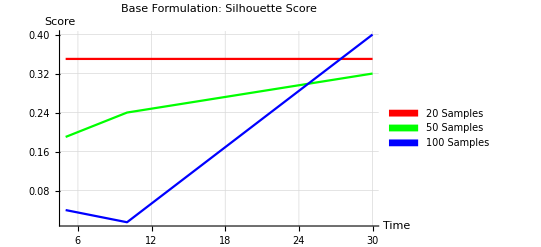

ListPlot::lpn: TagBox[RowBox[{\"(\", \"\", GridBox[{{\"5.\", \"703.16\"},{\"10.\", \"703.16\"},{\"30.\", \"703.16\"}
   },GridBoxAlignment->{\"Columns\" -> {{Center}}, \"Rows\" -> {{Baseline}}},GridBoxSpacings->{\"Columns\" -> {Offset[0.28], {Offset[0.7]}, Offset[0.28]}, \"Rows\" -> {Offset[0.2], {Offset[0.4]}, Offset[0.2]}}], \"\", \")\"}],Function[BoxForm`e$, MatrixForm[BoxForm`e$]]] is not a list of numbers or pairs of numbers.

```mathematica
Legended[
Show[splot20,splot50, splot100,
PlotLabel-> "Base Formulation: Silhouette Score",
AxesLabel-> {"Time", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[{Red, Green, Blue}, {"20 Samples", "50 Samples", "100 Samples"}]
]
```

```mathematica
(* Base Tabu Homogeneity Scores *)
```

```mathematica
hscoreData20 = {{5, 0.36}, {10, 0.36}, {30, 0.36}};
hscoreData50 = {{5, 0.16}, {10, 0.22}, {30, 0.33}};
hscoreData100 = {{5,0.01}, {10,0.05}, {30, 0.009}};

hplot20= ListLinePlot[hscoreData20,
PlotStyle-> {Red}];
hplot50= ListLinePlot[hscoreData50,
PlotStyle-> {Green}];
hplot100= ListLinePlot[hscoreData100,
PlotStyle-> {Blue}];
```

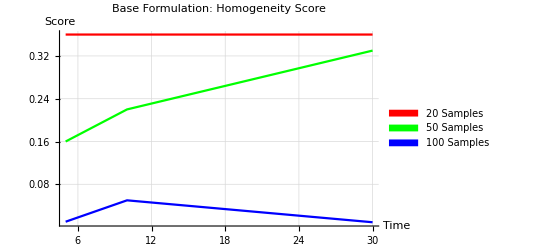

```mathematica
Legended[
Show[hplot20,hplot50, hplot100,
PlotLabel-> "Base Formulation: Homogeneity Score",
AxesLabel-> {"Time", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[{Red, Green, Blue}, {"20 Samples", "50 Samples", "100 Samples"}]
]
```

```mathematica
(* Base Tabu Completness Score *)

cscoreData20={{5,0.38},{10,0.38},{30,0.38}};
cscoreData50={{5,0.18},{10,0.26},{30,0.33}};
cscoreData100={{5,0.19},{10,0.07},{30,0.19}};
```

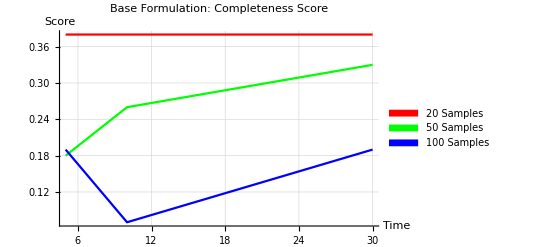

```mathematica
cplot20= ListLinePlot[cscoreData20,
PlotStyle-> {Red}];
cplot50= ListLinePlot[cscoreData50,
PlotStyle-> {Green}];
cplot100= ListLinePlot[cscoreData100,
PlotStyle-> {Blue}];


Legended[
Show[cplot20,cplot50, cplot100,
PlotLabel-> "Base Formulation: Completeness Score",
AxesLabel-> {"Time", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[{Red, Green, Blue}, {"20 Samples", "50 Samples", "100 Samples"}]
]
```

```mathematica
(* Base Tabu V-Measure *)
```

```mathematica
vscoreData20 = { {5,0.37}, {10,0.37},{30, 0.37}};
vscoreData50 = { {5,0.17}, {10,0.24}, {30,0.33}};
vscoreData100 = { {5,0.01},{10,0.06}, {30,0.018}};
```

```mathematica
vplot20= ListLinePlot[cscoreData20,
PlotStyle-> {Red}];
vplot50= ListLinePlot[cscoreData50,
PlotStyle-> {Green}];
vplot100= ListLinePlot[cscoreData100,
PlotStyle-> {Blue}];
```

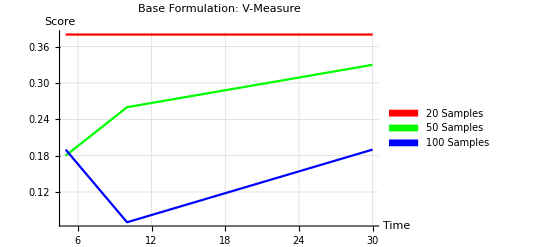

```mathematica
Legended[
Show[vplot20,vplot50, vplot100,
PlotLabel-> "Base Formulation: V-Measure",
AxesLabel-> {"Time", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[{Red, Green, Blue}, {"20 Samples", "50 Samples", "100 Samples"}]
]
```

```mathematica
(* Simulated Annealing *)
```

```mathematica
simInertia={ {20,546.67},{30,1465.74},{35,3057.51},{40,3921.44},{45,5525.67}};
simSil={ {20, 0.13},{30, -0.15},{35,-0.06},{40,-0.02},{45,-0.10}};
simHomog={ {20,0.20},{30,0.10},{35,0.03},{40,0.27},{45,0.03}};
simComp={{20,0.20},{30,0.10},{35,0.03},{40,0.28},{45,0.04}};
simV={{20,0.20},{30,0.10},{35,0.03},{40,0.27},{45,0.03}};
```

```mathematica
(* Sim Anneal Inertia *)
```

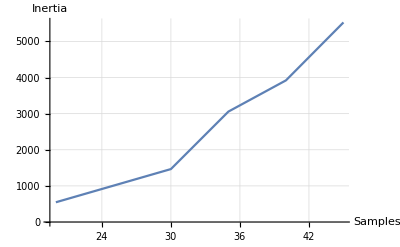

```mathematica
ListLinePlot[simInertia,
(* PlotLabel-> "Base Formulation: Simulated Annealing Cluster Inertia", *)
AxesLabel->{"Samples", "Inertia"},
GridLines->Automatic,
PlotRange->Automatic]
```

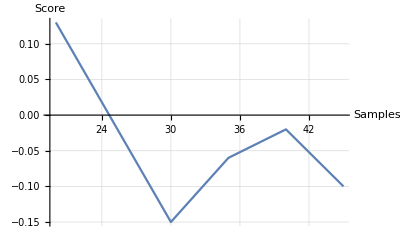

```mathematica
(* Sim Anneal Silhouette *)

ListLinePlot[simSil,
(* PlotLabel-> "Base Formulation: Simulated Annealing Silhouette Score", *)
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic]
```

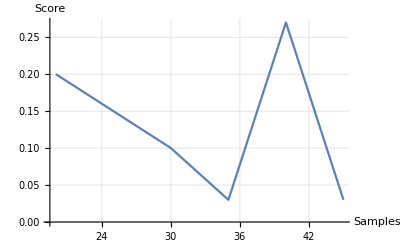

```mathematica
(* Sim Anneal Homogeneity *)

ListLinePlot[simHomog,
(* PlotLabel-> "Base Formulation: Simulated Annealing Homogeneity", *)
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic]
```

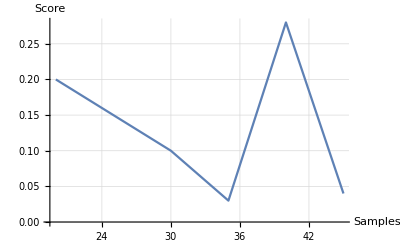

```mathematica
(* Sim Anneal Completenes *)

ListLinePlot[simComp,
(* PlotLabel-> "Base Formulation: Simulated Annealing Completeness Score", *)
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic]
```

```mathematica
(* Sim Anneal V-Measure *)

ListLinePlot[simV,
(* PlotLabel-> "Base Formulation: Simulated Annealing V-Measure", *)
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic]
```

-Graphics-